Evaluate the whole notebook first.(CRTL+A, then SHIFT+ENTER, or try Evaluation>>Evaluate Notebook)

## Table of Contents

#### Preparation

#### Visualization of Function

#### Import Data

#### Visualization of Data

#### Differentiation

#### Solve An Equation

# Why Mathematica

## Some example to show Mathematica can be useful in daily life, for Geeks of course.

## What is Mathematica

Well, just check this link out. http://www.wolfram.com/mathematica/

## What are we going to do

Information, which you recieve and deal with everyday, is an necessity for lief. So we are going to show you is how to process and present data with the help of Mathematica.

## Let’s move

### Preparation

#### What do you have to know about Mathmatica before we start

What is a notebook?
A notebook is a file ending with “.nb”. Right now, what you are reading is a notebook.

What is a cell?
Each cell has a square bracket on its right side. Cell can be put inside cells.
What I want you to know is that each can be formatted individually. Choose Format>>Style to format a cell. Or follow the advanced methods provided in documentation.

What is the use of different kinds of cells?
Just try it yourself. Cells are very import when writing and document. Mathematica is a good tool for word precessing, especially for scientific subjects.

What do you mean by documentation here?
Mathematica’s documentation can be find at Help>>Documentation. Once you start to work with mathematica, you will find that they have written a marvelous documentation for Mathematica.

#### What else

Lets start with several documentation pages. For example,

guide/DataVisualization

Keep using the Documentation Center in the Help menu, for that is really the best reference book.

Sometimes I do not want to move my mouse or something, I use the following command just inside the notebook to get help. Try them yourself. (Notes: Output is immediately printed below your codes if no hiding results commands are used.)

One question mark before a function or command to find the usage.

```mathematica
?Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

Use two question marks to get more information.

```mathematica
??Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

Attributes[Plot]={HoldAll,Protected}
 
Options[Plot]={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→System`Private`$Evaluated,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

### Visualization of Function

Function visualization is an important function of Mathemtica.

画图嘛，基本上是三种，一种是把函数可视化，一种是数据可视化，还有一种是绘制几何图形。

我们先来说一下函数可视化。

Mathematica 里面函数作图的函数基本上就是
Plot[]
LogPLot[]
Plot3D[]
ContourPlot[]
ContourPlot3D
DensityPlot[]
ParametricPLot[]
ParametricPlot3D[]
PolarPlot[]
DiscretePlot[]
DiscretePlot3D[]
ListPlot[]
ListLinePlot[]

（ 更多的内容可以在 Documentation 里面搜索 FunctionVisualization 获得。）

我们先从最基本的 Plot[] 开始吧。
比如我们要画函数 SIn[x]​Cos[x] 的图。（可能你已经注意到了，Mathemtica 里面的函数的自变量是用 [] 来括起来的，而且，内置函数是大写，所以当你自定义函数的时候，最好别用大写字母开头。）

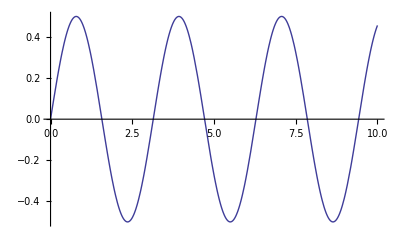

```mathematica
Plot[Sin[x]Cos[x],{x,0,10}]
```

简单吧，只需要把要做图的函数和做图时自变量的范围​给出来就行了。这里面
Sin[x]Cos[x]
是做图的函数。
{x,0,10}
是做图的自变量范围。

怎么样？是不是图做出来不需要自己修整就挺漂亮的？

哦，没有标出横轴纵轴是什么？这简单。看：

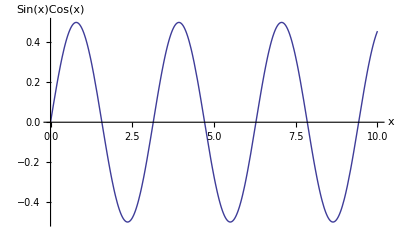

```mathematica
Plot[Sin[x]Cos[x],{x,0,10},AxesLabel->{"x","Sin(x)Cos(x)"}]
```

只需要一个命令，就可以了。
AxesLabel->{“x”, “Sin(x)Cos(x)”}
为什么要用引号把这些引起来呢？因为如果不加引号，这个是要被计算的。

横纵轴的标签字体太小？​

等等，大哥，有个问题啊。不能每次想要加一点点修改就得重新打一遍整个函数吧！
Bingo！这个问题太好了。Mathematica 当然不会这么傻。你可以直接在原来的代码里面改嘛，改了再 Shift+Enter 或者小键盘 Enter 运行一遍这个 Cell 就行了。
不过，要是想保留原来的图，再画一个呢？方法很简单，我们有个函数叫做 Show[]。 怎么用呢？
我们要习惯性的给自己画的图起个名字。比如

```mathematica
vofPlot0=Plot[Sin[x]Cos[x],{x,0,10}]
```

-Graphics-

​这样我们就给这个图起了个名字叫做 
vofPlot0
然后我们可以动用 Show[] 的力量啦！

```mathematica
Show[vofPlot0,AxesLabel->{Style["x",15,Bold,Orange],Style["Sin(x)Cos(x)",15,Bold,Green]}]
```

-Graphics-

这样我们就给这个图起了个名字叫做 
vofPlot0
然后我们可以动用 Show[] 的力量啦！（别往了，你随时可以通过 Documentation 来查看帮助的。你现在就可以查看 Show 的帮助。）
咦？奇怪啦，为什么 Show 里面的这个 AxesLabel 是 Plot 的选项啊？
是啦，Show 里面的选项是 Plot 的! Plot 的选项大都可以用的！

那这里面的 
Style[“x”, 15, Bold, Orange]
是什么意思啊？
你可以去查 Documentation 啦。不过我也说一下吧。
“x” 是我们的横轴标签，15 是字号，Bold 是说我们要用粗体，Orange 是说我们的字体的颜色是 橘色。

那，如果我们想要给图像加个标题么？

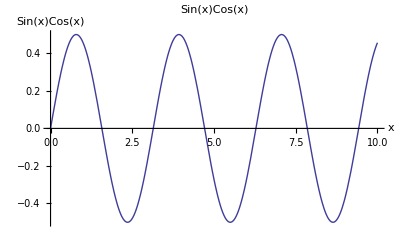

```mathematica
Show[vofPlot0,AxesLabel->{Style["x",12,Bold,Orange],Style["Sin(x)Cos(x)",12,Bold,Orange]},PlotLabel->Style["Sin(x)Cos(x)",12,Bold,Purple]]
```

怎么样？只需要一个
PlotLabel->”Sin(x)Cos(x)”
就搞定啦。如果想要改变字体，可以​跟上面给轴加标签一样，使用 Style.

“我就是觉得蓝色很丑”。好吧，我们可以换一下其它颜色。
怎么改呢？我们查了 Plot[]，发现里面有个 PlotStyle 选项，可以改颜色。好吧，我们借用 Show 吧。

```mathematica
Show[vofPlot0,AxesLabel->{Style["x",12,Bold,Orange],Style["Sin(x)Cos(x)",12,Bold,Orange]},PlotLabel->Style["Sin(x)Cos(x)",12,Bold,Purple],PlotStyle->Red]
```

-Graphics-

发现错误！好啊，正好认识一下错误吧。Mathematica 里面有很棒的颜色标记体系，用不同的颜色来代指不同的含义，这里红的框框就是说出错啦。还要注意我们输入代码时函数的颜色，选项的颜色，数字的颜色，这些自己先看一下吧。后面我们会讲。

那好吧，我没有好的解决办法。我一般都是直接在 Plot 里面改。就是这样：

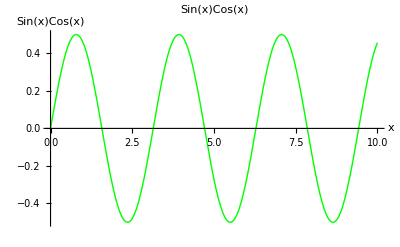

```mathematica
Plot[Sin[x]Cos[x],{x,0,10},AxesLabel->{Style["x",12,Bold,Orange],Style["Sin(x)Cos(x)",12,Bold,Orange]},PlotLabel->Style["Sin(x)Cos(x)",12,Bold,Purple],PlotStyle->Green]
```

好啦。

### Import Data

为了能够处理数据，首先要把数据拿过来，导入到这个 notebook 中才好用嘛。所以数据处理第一步呢，就是看看如何把我们的实验数据放到这个笔记本中来。

#### Data input manually.

如果数据很少呢，可以直接手动的把数据打到 notebook 中。例如：

```mathematica
data={{0.00,0.00},{1.00,2.00},{2.00,4.01},{3.00,6.05},{4.00,7.85},{5.00,9.70},{6.00,11.83},{7.00,13.75},{8.00,16.02},{9.00,17.86}}
```

{{0.,0.},{1.,2.},{2.,4.01},{3.,6.05},{4.,7.85},{5.,9.7},{6.,11.83},{7.,13.75},{8.,16.02},{9.,17.86}}

解释一下。这个 data 是用花括号来括起来的一些数据。这就是给这堆数据起了个名字叫 data ，以后呢，data 就代表这堆数据了。
如果看不出来这堆数据是什么样子呢，可以用 MatrixForm 来看看到底数据出如何存在的。

```mathematica
data//MatrixForm
```

(0. | 0.
1. | 2.
2. | 4.01
3. | 6.05
4. | 7.85
5. | 9.7
6. | 11.83
7. | 13.75
8. | 16.02
9. | 17.86)

这里又出现一种新的函数用法：//。上面那个语法等价于 MatrixForm[data] 的。有时候只是写草稿，不停的改动，用 // 加在末尾要比找位置加方括号要方便。

简单吧，把数据都录入进来，给它起个名字。然后运行。

但是，有时候我不想在我运行了这个 Cell 之后再出来一大堆输出，这时候可以在语句末尾加一个 ； ，类似 Matlab。例如：

```mathematica
data={{0.00,0.00},{1.00,2.00},{2.00,4.01},{3.00,6.05},{4.00,7.85},{5.00,9.70},{6.00,11.83},{7.00,13.75},{8.00,16.02},{9.00,17.86}};
```

要注意一点的是，当我们重新对 data 这个变量赋值的时候，是没有提醒的！

#### Data from a file.

很多时候我们是把数据放在文件中的，即我们要处理一个数据文件中的数据。这样我们就需要用的 Import[] 这个函数了了。

```mathematica
(* SetDirectory["D:\\Kuaipan\\Other\\GEEK\\WhyMathematica"]; *)(* 这里是目录设定，暂时可以不用，所以注释掉了。顺便说下如何注释。注释就是这样用括号和星花来包括起来的。 *)
```

```mathematica
dataimport=Import["Data/SimpleData.dat"]
(* 这里用的是 / ，如果是 windows 系统，请使用 \\ 来代替这里的 /。 *)
```

{{0.,0.},{1.,2.},{2.,4.01},{3.,6.05},{4.,7.85},{5.,9.7},{6.,11.83},{7.,13.75},{8.,16.02},{9.,17.86}}

大家可以看到，这个从文件中导入跟前面是类似的。只不过数据文件不同的写法可能导致导入的数据存放方法的不同。
导入的路径问题，可以参考上面的语句中的注释。

#### More about importing data

之前我们把数据导入进来并且给数据起了个名字。那么如果我们想要取出数据的一部分来看看呢？
前面说过这些数据的格式是 tables，我们可以按照 table 的语法来处理这些数据。（请使用 Documentation。）

举个例子。取出数据的第二个元素：

```mathematica
data[[2]]
```

{1.,2.}

我们看到 data 的第二个元素还是有结构的，我们可以再使用一次这个技能，取出第二个元素的第一个元素：

```mathematica
data[[2]][[1]]
```

1.

或者可以用更简单些的写法：

```mathematica
data[[2,1]]
```

1.

我们可以轻松的计算数据的长度：

```mathematica
len=Length[data]
```

10

上面我们计算了数据的长度并把长度值给了 len。这样以后再想使用这个长度值的时候就可以直接输入 len。

```mathematica
len
%
```

10

10

上面的 % 是啥？% 的作用是取回最近的一个输出。看上面的例子就挺明确了。
更多内容请查看 Documentation Center。

### Visualization of Data

有了数据，我们常常需要做可视化。

对于这些散点，我们可以使用 ListPlot[] 函数。

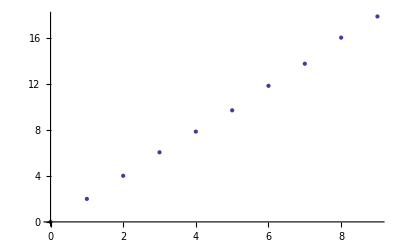

```mathematica
plt0=ListPlot[data]
```

但是有时候我们不喜欢这个图，因为不完整。所以我们要像之前函数可视化里面那样对图进行改造。
比如加上横纵坐标的标签：

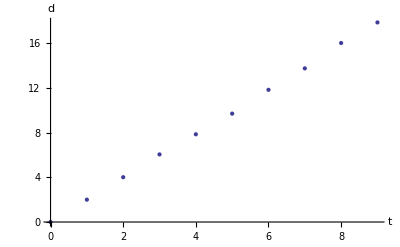

```mathematica
plt1=ListPlot[data,AxesLabel->{t,d}]
```

同样，类似之前函数可视化，还可以改变标签文字的样式：

```mathematica
plt2=ListPlot[data,AxesLabel->{Style[t,15,Bold,Orange],Style[d,15,Bold,Green]}]
```

-Graphics-

我们还有 Show[] 的强大能力。
例如我们可以把横纵轴的刻度标签变成加粗：

```mathematica
plt3=Show[plt1,LabelStyle->{Bold}]
```

-Graphics-

改变大小：

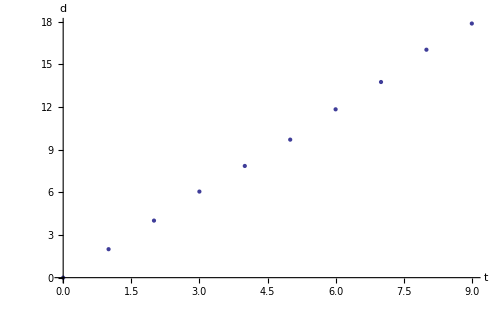

```mathematica
plt4=Show[plt1,LabelStyle->{Bold},ImageSize->500]
```

添加 frames ：

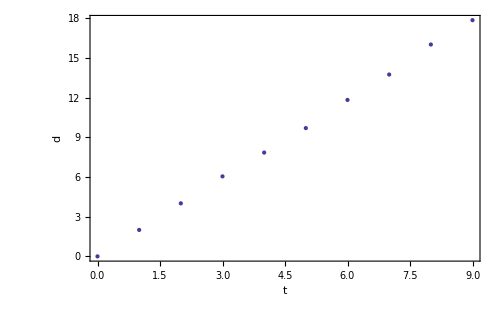

```mathematica
plt5=Show[plt1,LabelStyle->{Bold},Frame->True,FrameLabel->{Style[t,15,Bold,Orange],Style[d,15,Bold,Green]},ImageSize->500]
```

如果我们想把数据点连起来呢？我们来试试：

```mathematica
plt6=Show[plt1,LabelStyle->{Bold},Joined->True,Frame->True,FrameLabel->{Style[t,15,Bold,Orange],Style[d,15,Bold,Green]},ImageSize->500]
```

-Graphics-

好吧，失败了。为什么呢？因为 Joined 是 ListPlot 的一个选项，不是全局的。

那我们再试试：

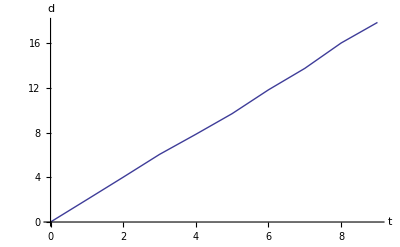

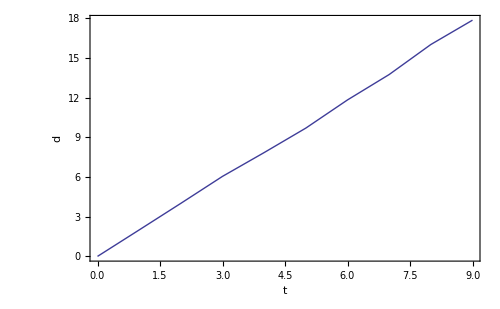

```mathematica
plt7=ListPlot[data,AxesLabel->{Style[t,15,Bold,Orange],Style[d,15,Bold,Green]},Joined->True]
plt8=Show[%,LabelStyle->{Bold},Frame->True,FrameLabel->{Style[t,15,Bold,Orange],Style[d,15,Bold,Green]},ImageSize->500]
```

太坏了，Joined 之后就看不到数据点了。这时候可以用 PlotMarkers ：

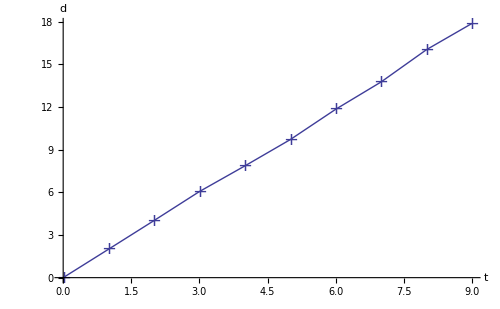

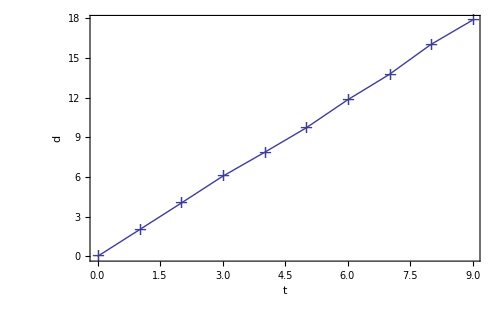

```mathematica
plt9=ListPlot[data,AxesLabel->{Style[t,15,Bold,Orange],Style[d,15,Bold,Green]},Joined->True,PlotMarkers->{"+"}]
plt10=Show[%,LabelStyle->{Bold},Frame->True,FrameLabel->{Style[t,15,Bold,Orange],Style[d,15,Bold,Green]},ImageSize->500]
```

#### DATA FITTING?

Mathematica 是一个用来做数据拟合的一个很优秀的工具。

数据拟合：

```mathematica
line = Fit[data, {1,t},t]
```

-0.00490909+1.98042 t

画出这段曲线：

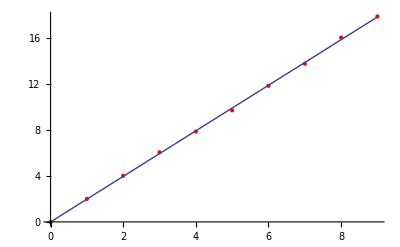

```mathematica
Show[ListPlot[data, PlotStyle->Red], Plot[line, {t, 0, 9}]]
```

拟合结果：

```mathematica
fitting=LinearModelFit[data,{1,t},t]
```

FittedModel[-0.00490909+1.98042 t]

```mathematica
fitting["BestFit"]
```

-0.00490909+1.98042 t

```mathematica
fitting[{"RSquared","FitResiduals","ANOVATable"}]
```

{0.999665,{0.00490909,0.0244848,0.0540606,0.113636,-0.0667879,-0.197212,-0.0476364,-0.108061,0.181515,0.0410909}, | DF | SS | MS | F-Statistic | P-Value
t | 1 | 323.572 | 323.572 | 23880.9 | 3.43948×10^-15
Error | 8 | 0.108395 | 0.0135494 |  | 
Total | 9 | 323.68 |  |  | }

关于数据拟合，这是个小入门。更多的内容以后会添加。

另外，了解数据拟合的函数，可以阅读 Documentation Center 的 ManipulatingNumericalData 教程，或者 CurveFitting 教程。

### Differentiation

#### 基础

用 Mathematica 求导数，也是一件很容易的事情。

基本上而言，只需要知道一个函数就行了：

```mathematica
D[x^2,x]
```

2 x

D[] 就是用来求导数的。上面的例子中，我们是将 x^2 对 x 求导数的，所以结果是 2x 。
可以看到，要求导的函数放在逗号前面，自变量放在逗号后面。
再看一个例子：

```mathematica
D[Sin[x],x]
```

Cos[x]

那么我们要求一个函数关于 x 的二阶导数呢？例子：

```mathematica
D[x^2,{x,2}]
```

2

```mathematica
D[Sin[x],{x,2}]
```

-Sin[x]

要求 n 阶导数就用 n 来代替上面的 2 。

如果是多变量微分，那么就把所有要求导数的自变量都放在函数后面，即：

```mathematica
D[42 x^2+9 y^2,{{x,y}}]
```

{84 x,18 y}

总之，模仿就行了。可是为什么要加两个花括号呢？看了下面的例子就明白了。

```mathematica
D[42 x^2+9 y^2,{{x,y},2}]
```

{{84,0},{0,18}}

明白了吧，如果不加花括号的话，怎么表述求 Hessian 矩阵（Wikipedia）呢？

那为什么结果里面最外面会带个或括号啊，因为 Hessian 矩阵的结果是要嵌套再的啊，如果没有花括号，容易混乱了。

好嘛，那我算出了一个结果，比如

```mathematica
D[42 x^2+9 y^2,{{x,y}}]
```

{84 x,18 y}

我只想要第一部分，怎么办呢？
这就又用到了 table 的操作了。方法是

```mathematica
D[42 x^2+9 y^2,{{x,y}}][[1]]
```

84 x

直接对结果操作也可以：

```mathematica
{84 x,18 y}[[1]]
```

84 x

#### 自己定义函数

有时候需要自己定义一个函数，比如我想给 Sin[x]+Sin[x]+Cos[x]+Tan[x]+Cot[x]+Sinh[x]+Cosh[x] 起个名字叫做 differentiationF1[x] 。
操作方法是：

```mathematica
differentiationF1[x_]=Sin[x]+Sin[x]+Cos[x]+Tan[x]+Cot[x]+Sinh[x]+Cosh[x]
```

Cos[x]+Cosh[x]+Cot[x]+2 Sin[x]+Sinh[x]+Tan[x]

就是自变量后面加上 _ 来标示出来。
大家注意到了一点，就是上面的定义直接进行了运算，并显示了结果。有时候我们不想离开运算并得到结果。这时候就要用到延迟功能：

```mathematica
differentiationF1[x_]:=Sin[x]+Sin[x]+Cos[x]+Tan[x]+Cot[x]+Sinh[x]+Cosh[x]
```

就是在等号前面加 ： 。这样定义出来的就会在第一次用的时候才运算。

我们既然是学习求导的，自然要对这个自己定义的函数求一次导数。

```mathematica
D[ differentiationF1[x],{x}]
```

2 Cos[x]+Cosh[x]-Csc[x]^2+Sec[x]^2-Sin[x]+Sinh[x]

其实跟上一部分没啥区别。

### Solve an equaiton

Mathematica is originally developed for algebra, Equation solving is one of the virtues of Mathematica.

Search “equation solving” in documentation center.

#### Solve

As an example, I would like to solve a very simple equaiton. Suppose we have an equaiton

```mathematica
eqns={x+y==2,x-y==1}
```

{x+y==2,x-y==1}

```mathematica
eqnssol=Solve[eqns]
```

{{x→3/2,y→1/2}}

Now we get a table. Extract the elements

```mathematica
{x,y}/.eqnssol[[1]]
```

{3/2,1/2}

Why is that? “/.” is the simbol of replacement. That means we can replace something using “/.”. For example, we would like to replace temp with 1

```mathematica
temp/.{temp->1}
```

1

#### Differential equations

Differential equaitons are the most commonly used equations in physical system.

Search “differential equation” in documentation center and read them.

Examples,